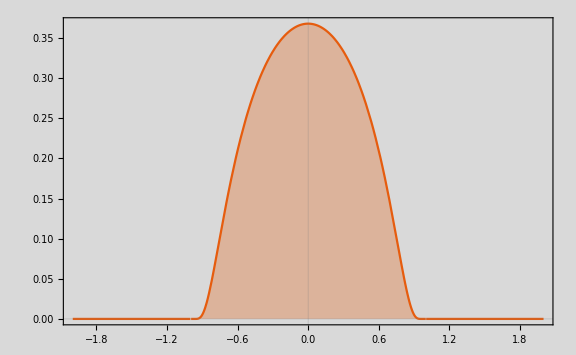

```mathematica
f[x_]=Piecewise[{{Exp[1/(x^2-1)],Abs[x]<1},{0, Abs[x]≥1}}];
Plot[f[x],{x,-2,2},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray]
```

```mathematica
Export["/home/martin/Documents/utfsm/EACI/Docs/bump.png",%17,"PNG"]
```

/home/martin/Documents/utfsm/EACI/Docs/bump.png

```mathematica
g[x_,y_]=f[x]*f[y];
Plot3D[g[x,y],{x,-2,2},{y,-2,2},PlotRange->All,ImageSize->Large,PlotTheme->"Scientific", Background->LightGray]
```

-Graphics3D-

```mathematica
Export["/home/martin/Documents/utfsm/EACI/Docs/3dbump.png",%29,"PNG"]
```

/home/martin/Documents/utfsm/EACI/Docs/3dbump.png

Piecewise[{{0, x≤0}, {ⅇ^(-1/x)/(ⅇ^(-1/(1-x))+ⅇ^(-1/x)), 0<x<1}, {1, 1≤x≤2}, {ⅇ^(-1/(3-x))/(ⅇ^(-1/(3-x))+ⅇ^(-1/(-2+x))), 2<x<3}, {0, True}}]

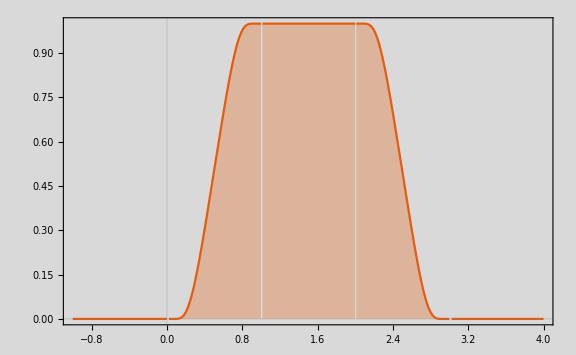

```mathematica
g[x_]=Exp[(-1/x)];
h[x_]=g[x]/(g[x]+g[1-x]);
d[x_]=Piecewise[{{0,x<=0},{h[x],0<x<1},{1,1≤x≤2},{h[-(x-3)],2<x<3},{0,x≥3}}]
Plot[d[x],{x,-1,4},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

```mathematica
Export["/home/martin/Documents/utfsm/EACI/Docs/construction.png",%105,"PNG"]
```

/home/martin/Documents/utfsm/EACI/Docs/construction.png